# SETA ROLL NO. 24020570026 QUESTION 1 secant method

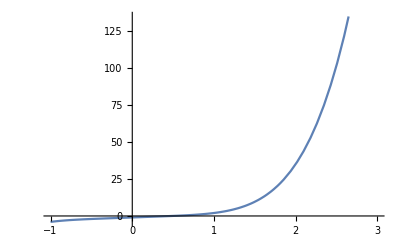

```mathematica
f[x_]= x^5+2*x-1;
Plot[f[x],{x,-1,3}]
```

```mathematica
x0=0;
x1=1;
Nmax=10;
eps=10^(-6);
Print["f[x]=",f[x]];
For[i=1,i≤Nmax,i++,
x2=N[x1-(f[x]/.x->x1)*(x1-x0)/((f[x]/.x->x1)-(f[x]/.x->x0))];
If[Abs[x1-x2]<eps,Return[x2],x0=x1;x1=x2];
Print["In",i,"th Number of iterations the root is :",x2];
Print["estimated error is :",Abs[x1-x0]]];
Print["root is :",x2];
Print["estimated error is:",Abs[x2-x1]];
```

f[x]=-1+2 x+x^5

In1th Number of iterations the root is :0.333333

estimated error is :0.666667

In2th Number of iterations the root is :0.427562

estimated error is :0.0942285

In3th Number of iterations the root is :0.489511

estimated error is :0.0619495

In4th Number of iterations the root is :0.486304

estimated error is :0.00320717

In5th Number of iterations the root is :0.486389

estimated error is :0.0000846951

Return[0.486389]

root is :0.486389

estimated error is:1.34318×10^-7

## question 2 gauss seidal

```mathematica
GaussSeidel[A0_,b0_,X0_,maxtier_]:=Module[{A=N[A0],b=N[b0],xk=X0,xk1,i,j,k=0,n,m,OutputDetails},size=Dimensions[A];
n=size[[1]];
m=size[[2]];
If[n≠m,Print["Not a square matrix, cannot proceed with Gauss se method"];
Return[]];
OutputDetails={xk};
xk1=Table[0,{n}];
While[k<maxtier,For[i=1,i≤n,i++,xk1[[i]]=(1/A[[i,i]])*(b[[i]]-Sum[A[[i,j]]*xk[[j]],{j,1,i-1}]-Sum[A[[i,j]]*xk[[j]],{j,i+1,n}])];
k++;
OutputDetails=Append[OutputDetails,xk1];
xk=xk1;];
colHeading=Table[X[s],{s,1,n}];
Print[NumberForm[TableForm[OutputDetails,TableHeadings->{None,colHeading}],6]];
Print["No. of iterations performed = ",maxiter];];

A={{5,1,-2},{3,4,-1},{2,-3,5}};
b={2,-2,10};
X0={0,0,0};

GaussSeidel[A,b,X0,10]
```

X[1] | X[2] | X[3]
0 | 0 | 0
0.4 | -0.5 | 2.
1.3 | -0.3 | 1.54
1.076 | -1.09 | 1.3
1.138 | -0.982 | 0.9156
0.96264 | -1.1246 | 0.9556
1.00716 | -0.98308 | 0.940184
0.97269 | -1.02032 | 1.00729
1.00698 | -0.977695 | 0.99873
0.995031 | -1.00555 | 1.01059
1.00535 | -0.993625 | 0.998656

No. of iterations performed = maxiter

## question 3 simpsons

Table::iterb: Iterator {i,1,$Canceled} does not have appropriate bounds.

```mathematica
a=Input["Enter the left end point :"];
b=Input["Enter the right end point :"];
n=Input["Enter the number of sub intervals to be formed :"];
h=(b-a)/n;
y=Table[a+i*h,{i,1,n}];
f[x]:=x/x^3+10;
sumodd=0;
sumeven=0;
For[i=1,i<n,i+=2,sumodd+=4*f[x]/.x->y[[i]]];
For[i=2,i<n,i+=2,sumeven+=2*f[x]/.x->y[[i]]];
Sn=(h/3)*((f[x]/.x->a)+N[sumodd]+N[sumeven]+(f[x]/.x->b));
Print["For n=",n,",Simpson estimate is: ",Sn] in=NIntegrate[x/x^3+10,{x,0,1}];
Print["True value is ",in] Print["Absolute error is ",Abs[Sn-in]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.22413×10^-225}. NIntegrate obtained 8.5826391230823317424901377733077753396213277675075603181991970147×10^27949 and 8.5826391230823317424901377733077753396213277675075603181991970147×10^27949 for the integral and error estimates.

For n=7,Simpson estimate is: 76.2337

Set::write: Tag Times in in Null is Protected.

True value is in

Absolute error is Abs[76.2337-in]

Null^2

## ques 4 lagrange method

```mathematica
LagrangePolynomial[x0_,f0_]:=
Module[{xi=x0,fi=f0,n,m,polynomial},
n=Length[xi];
m=Length[fi];
If[n≠m,Print["List of Points and Function values are not of same size"];
Return[];];
For[i=1,i≤n,i++,
L[i,x_]=(Product[(x-xi[[j]])/(xi[[i]]-xi[[j]]),{j,1,i-1}])*(Product[(x-xi[[j]])/(xi[[i]]-xi[[j]]),{j,i+1,n}]);];
polynomial[x_]=Sum[L[k,x]*fi[[k]],{k,1,n}];
Return[polynomial[x]];]
```

```mathematica
nodes = {-1,2,4,5};
values = {-5,13,255,625};
lagrangePolynomial[x_] = LagrangePolynomial[nodes,values]
```

-1/18 (2-x) (4-x) (5-x)+13/18 (4-x) (5-x) (1+x)+51/2 (5-x) (-2+x) (1+x)+625/18 (-4+x) (-2+x) (1+x)